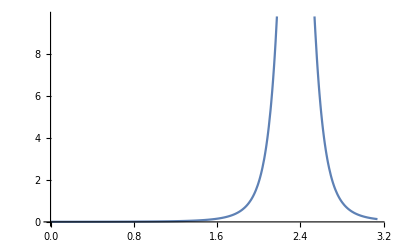

```mathematica
SetDirectory[FileNameJoin@{ParentDirectory[NotebookDirectory[]],"Shared"}];
Needs["gUtils`"];
Needs["gBRDF`"];
Needs["sgCommon`"];
Needs["gPlots`"];
Needs["gPlots3D`"];
Needs["gPlots3DEx`"];
Needs["gSphericalCap`"];
Needs["gTexStyles`"];
Needs["gBlochSphere`"];
ResetDirectory[];



testGGX[θ_]:=Module[
{},

viewDir={Cos[θ],Sin[θ]};
normalDir={0,1};
lightDir=Normalize@{1,1};
halfDir=Normalize[(viewDir+lightDir)/2];
noh=Dot[normalDir,halfDir];
gDGGX[0.1,noh]
];

Plot[testGGX[θ],{θ,0,π}]
```

```mathematica
gParamVaryDirectionDisbs[<|"lightDir"->({1,1}&),"viewDir"->({-1,1}&),"normalDir"->({0,1}&),"roughness"->0.3,"disbFunc"->(gDGGX[#roughness,#noh]&),"color"->RGBColor[1, 0.5, 0],"label"->"GGX Normal Lobe"|>,π/2]
```

<|lightDir→{1,1},viewDir→{-1,1},normalDir→{0,1},roughness→0.3,disbFunc→(gDGGX[#roughness,#noh]&),color→RGBColor[1, 0.5, 0],label→GGX Normal Lobe|>

0.0286479/(1-0.91 Clip[Normalize[{0,1}[<|θ→π/2|>]].Normalize[Normalize[{-1,1}[<|θ→π/2|>]]+Normalize[{1,1}[<|θ→π/2|>]]],{0,1}]^2)^2